## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.850/";
loadFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p3.850/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 ,0.0063 ,0.005 ,0.00385, 0.0031 ,0.0028, 0.0025 ,0.0022 ,0.002 ,0.0018,0.001 ,0.00067, 0.0005 ,0.0004, 0.00033,0.00025 ,0.00018 ,0.00014 ,0.00011 ,0.00010,.000091 ,0.000083, 0.000077 ,0.000071 ,0.000067,0.000054, 0.000045 ,0.000036};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000,0.00025000,0.00018000,0.00014000,0.00011000,0.00010000,0.00009100,0.00008300,0.00007700,0.00007100,0.00006700,0.00005400,0.00004500,0.00003600}

```mathematica
{"0.06300000","0.03900000","0.03105000","0.02500000","0.01600000","0.01000000","0.00800000","0.00630000","0.00500000","0.00385000","0.00310000","0.00280000","0.00250000","0.00220000","0.00200000","0.00180000","0.00100000","0.00067000","0.00050000","0.00040000","0.00033000","0.00025000","0.00018000","0.00014000","0.00011000","0.00010000","0.00009100","0.00008300","0.00007700","0.00007100","0.00006700"}
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000,0.00025000,0.00018000,0.00014000,0.00011000,0.00010000,0.00009100,0.00008300,0.00007700,0.00007100,0.00006700}

```mathematica
wtlist={80000.,90000.,100000.};
```

```mathematica
wtlist={0.,50000.,60000.,70000.,80000.,90000.,100000.};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlist
```

{80000.00,90000.00,100000.00}

```mathematica
wtlistLongest={10000.,10000.,10000.,10000.,10000.,10000.,10000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.8500_T",Tstring[[Length[Tlist]]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],{idx,0,0}];
```

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.8500_T",Tstring[[Length[Tlist]]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],{idx,0,2}];
```

```mathematica
timeLongest={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
time=timeLongest
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
SISF
```

{1,3}

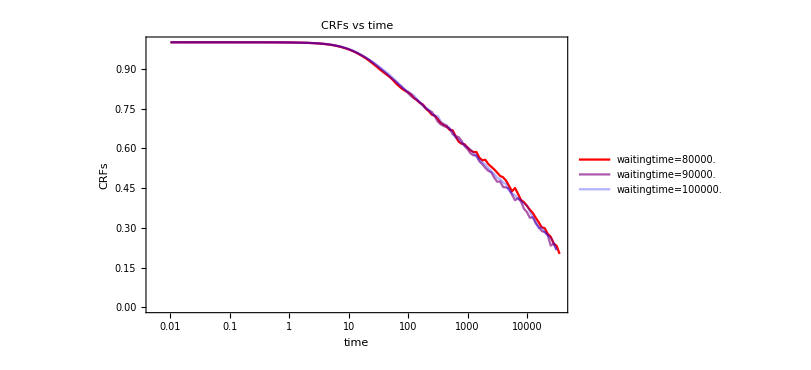

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[t]],SISF[[1,wt,2,t]]},{t,Length[SISF[[1,wt,2]]]-10}],{wt,Length[wtlist]}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[3],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,Length[wtlist]}],PlotRange->All]
```

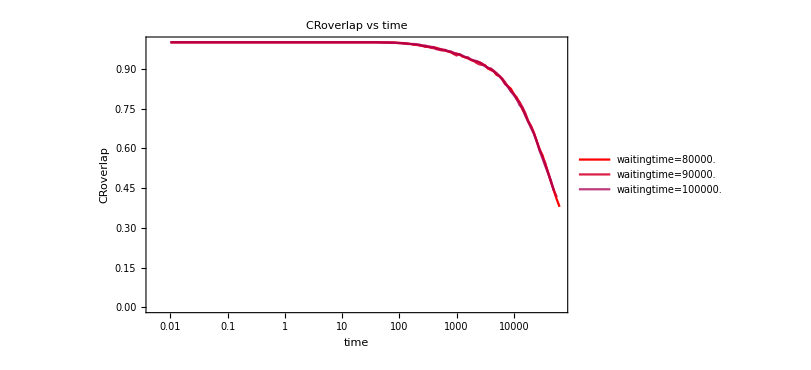

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-5}],{wt,3}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,3}],PlotRange->{All,{0,1}}]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlap=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/overlapCRoverlap_N4096_p3.8500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
Length[Tlist]
```

26

```mathematica
SISF=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.850/SISFCRSISF_N4096_p3.8500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,0}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapIndividual=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,1}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapMean=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
overlapMean=Table[Table[Mean[Table[overlap[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[Mean[Table[SISF[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[SISF[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p385/glassyDynamics_N4096_p3.8500_T",Tstring[[Length[Tlist]-8]],"_waitingTime",wtlistLongestString[[Length[Tlist]]],"_idx1.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

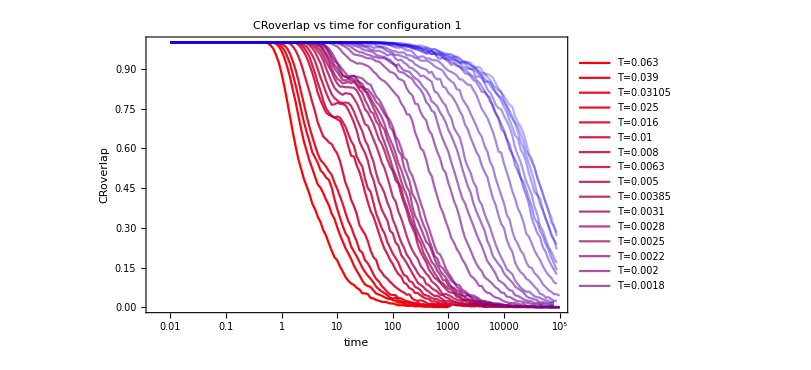

```mathematica
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapIndividual[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time for configuration 1",Joined->True]
```

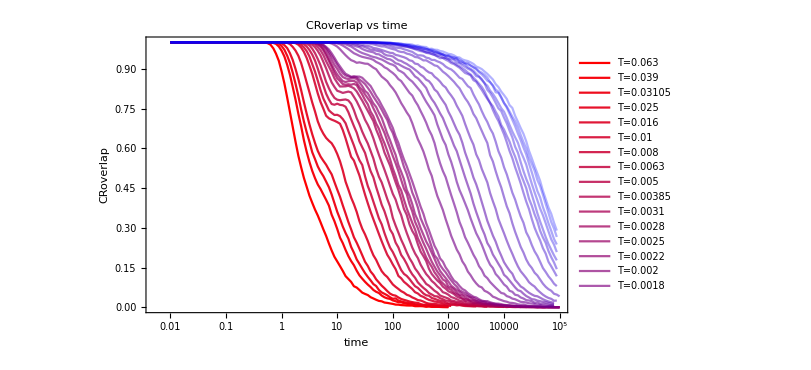

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
fitCROverlapStartNum={4.545633497156052,6.972324797990245,7.688430481846143,9.342191365655887,11.359328382212755,15.816075884439703,17.103424454731552,21.189518319840886,23.81560922495133,27.8367722375015,30.685453336137705,33.82312067339929,36.55834456391838,39.51772229179588,41.89421685655501,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,80.,80.,80.,80.,80.,80.,80.,80.,80.,80.};
```

```mathematica
fitCROverlapStartPos=Table[Position[time,_?(#>fitCROverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{45,48,49,51,53,55,56,58,59,60,61,62,63,63,64,65,65,65,65,65,65,70,70,70,70,70,70,70,70,70,70}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitCROverlapStartPos[[T]],Length[CRoverlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.999939 ⅇ^(-0.515545 t^0.519302)],FittedModel[0.999966 ⅇ^(-0.353184 t^0.541758)],FittedModel[0.999971 ⅇ^(-0.2793 t^0.568154)],FittedModel[0.999978 ⅇ^(-0.222379 t^0.586029)],FittedModel[0.999987 ⅇ^(-0.161697 t^0.593373)],FittedModel[0.999993 ⅇ^(-0.0907881 t^0.646466)],FittedModel[0.999995 ⅇ^(-0.0756969 t^0.649911)],FittedModel[0.999995 ⅇ^(-0.0587052 t^0.661151)],FittedModel[0.999996 ⅇ^(-0.0469572 t^0.66898)],FittedModel[0.999996 ⅇ^(-0.0360893 t^0.677554)],FittedModel[0.999997 ⅇ^(-0.0279403 t^0.691862)],FittedModel[0.999998 ⅇ^(-0.0266328 t^0.686269)],FittedModel[0.999998 ⅇ^(-0.0223404 t^0.698644)],FittedModel[0.999998 ⅇ^(-0.0206731 t^0.696748)],FittedModel[0.999998 ⅇ^(-0.0162701 t^0.717823)],FittedModel[0.999998 ⅇ^(-0.0162733 t^0.701715)],FittedModel[0.999999 ⅇ^(-0.00704847 t^0.736315)],FittedModel[0.999999 ⅇ^(-0.00444992 t^0.741402)],FittedModel[0.999999 ⅇ^(-0.00353361 t^0.725584)],FittedModel[0.999999 ⅇ^(-0.00267254 t^0.729492)],FittedModel[0.999999 ⅇ^(-0.00188821 t^0.741303)],FittedModel[0.999999 ⅇ^(-0.0014236 t^0.733621)],FittedModel[0.999998 ⅇ^(-0.000814249 t^0.752556)],FittedModel[0.999999 ⅇ^(-0.000641544 t^0.743966)],FittedModel[0.999995 ⅇ^(-0.000330518 t^0.778901)],FittedModel[0.999998 ⅇ^(-0.000380123 t^0.754086)],FittedModel[0.999184 ⅇ^(-0.000255802 t^0.781341)],FittedModel[0.999997 ⅇ^(-0.000285125 t^0.75924)],FittedModel[0.996343 ⅇ^(-0.00017472 t^0.794829)],FittedModel[0.998938 ⅇ^(-0.000234862 t^0.758329)],FittedModel[0.999044 ⅇ^(-0.000159593 t^0.78796)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{3.5816,6.82841,9.43977,13.0053,21.5555,40.9069,53.0556,72.844,96.7288,134.636,176.108,196.975,230.685,261.696,310.253,353.828,836.628,1485.58,2393.55,3366.77,4726.53,7589.61,12735.1,19568.5,29435.,34307.9,39568.6,46676.6,53411.3,61062.2,65880.6}

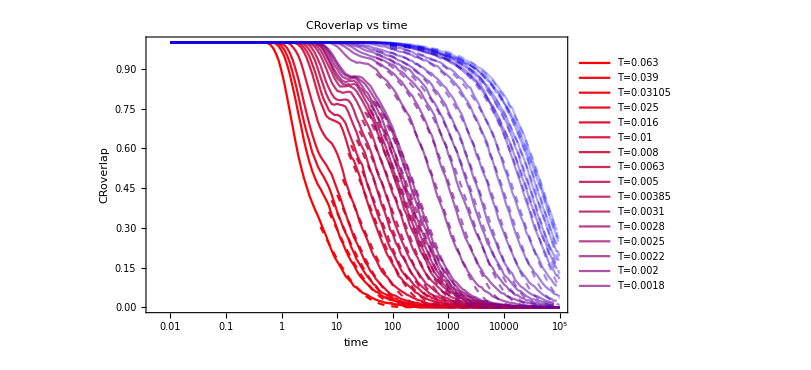

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

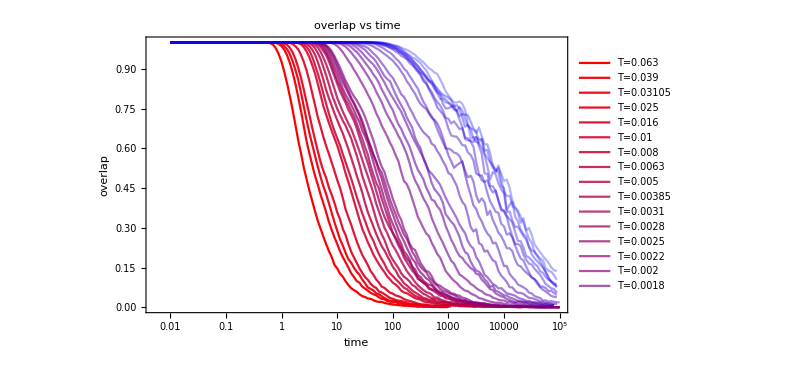

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
Log10[time[[66]]]
```

Part::partw: Part 66 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

Log[{0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧}⟦66⟧]/Log[10]

```mathematica
fitOverlapStartPos=fitCROverlapStartPos+8
```

{53,56,57,59,61,63,64,66,67,68,69,70,71,71,72,73,73,73,73,73,73,78,78,78,78,78,78,78,78,78,78}

```mathematica
{45,48,49,51,53,55,56,58,59,60,61,62,63,63,64,65,65,65,65,65,65,70,70,70,70,70}-10
```

{35,38,39,41,43,45,46,48,49,50,51,52,53,53,54,55,55,55,55,55,55,60,60,60,60,60}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β,c},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.998925 ⅇ^(-0.880722 t^0.370944)],FittedModel[0.99906 ⅇ^(-0.730777 t^0.367725)],FittedModel[0.999463 ⅇ^(-0.567867 t^0.411633)],FittedModel[0.999372 ⅇ^(-0.562359 t^0.390148)],FittedModel[0.999676 ⅇ^(-0.414012 t^0.425282)],FittedModel[0.999793 ⅇ^(-0.327558 t^0.423669)],FittedModel[0.999869 ⅇ^(-0.273158 t^0.440648)],FittedModel[0.999878 ⅇ^(-0.216337 t^0.465497)],FittedModel[0.999909 ⅇ^(-0.208124 t^0.452783)],FittedModel[0.999913 ⅇ^(-0.159898 t^0.479894)],FittedModel[0.999919 ⅇ^(-0.155677 t^0.458633)],FittedModel[0.99995 ⅇ^(-0.174383 t^0.439364)],FittedModel[0.999951 ⅇ^(-0.157876 t^0.446567)],FittedModel[0.999958 ⅇ^(-0.124417 t^0.476096)],FittedModel[0.999958 ⅇ^(-0.124152 t^0.463107)],FittedModel[0.999963 ⅇ^(-0.123782 t^0.455133)],FittedModel[0.99999 ⅇ^(-0.0492038 t^0.537099)],FittedModel[0.999996 ⅇ^(-0.0321897 t^0.560408)],FittedModel[0.999997 ⅇ^(-0.0361792 t^0.507843)],FittedModel[0.999998 ⅇ^(-0.0228716 t^0.551049)],FittedModel[0.999998 ⅇ^(-0.0248507 t^0.521444)],FittedModel[0.999988 ⅇ^(-0.0200756 t^0.510676)],FittedModel[0.999997 ⅇ^(-0.0114285 t^0.548515)],FittedModel[0.999999 ⅇ^(-0.0183021 t^0.468515)],FittedModel[0.999999 ⅇ^(-0.00865112 t^0.533056)],FittedModel[0.999999 ⅇ^(-0.00841239 t^0.523173)],FittedModel[0.999999 ⅇ^(-0.00658982 t^0.540317)],FittedModel[0.999999 ⅇ^(-0.00567871 t^0.544768)],FittedModel[0.999995 ⅇ^(-0.00555374 t^0.540925)],FittedModel[0.999998 ⅇ^(-0.00614291 t^0.524276)],FittedModel[1. ⅇ^(-0.00558764 t^0.529356)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{1.40833,2.34653,3.95386,4.37269,7.95333,13.9341,19.0105,26.8103,32.028,45.6069,57.712,53.2539,62.4043,79.6394,90.4598,98.5318,272.464,460.1,689.534,949.332,1194.93,2107.15,3471.29,5111.19,7413.19,9254.09,10883.1,13255.5,14775.7,16536.4,18017.2}

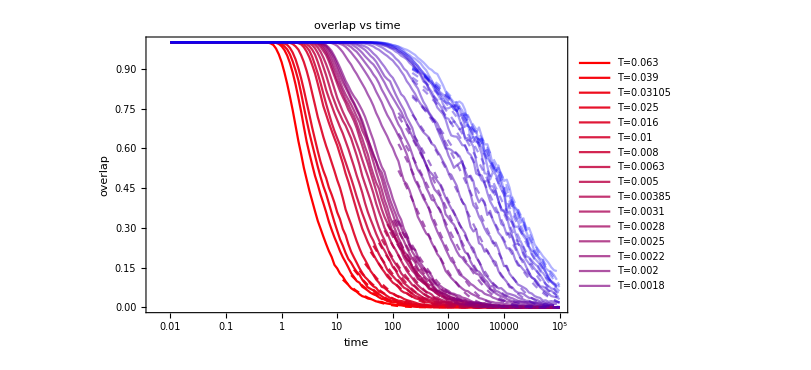

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

Show::gcomb: Could not combine the graphics objects in Show[CRoverlapfitST,CRoverlapLTPlot,{}].

#### CRSISF

```mathematica
SISF[[2,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

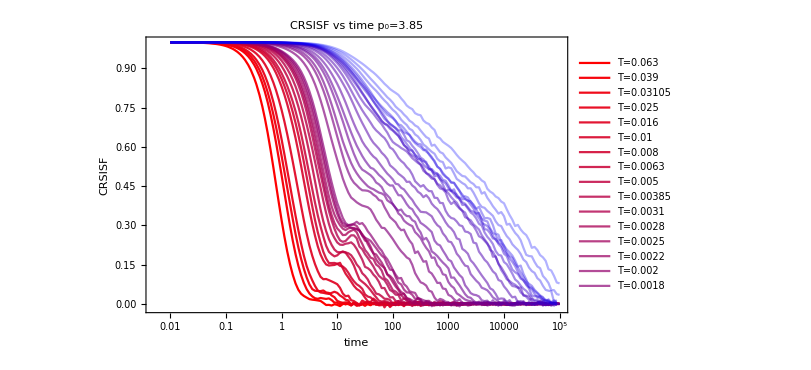

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISF[[T,1,2,rec]]},{rec,Length[SISF[[T,1,2]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time p_0=3.85",Joined->True]
```

```mathematica
fitCRSISFStartNum={4.337072420050368,7.194205862609111,7.931187148870541,11.041221920722247,12.41437888222547,15.092266119370647,17.301989581024966,20.62319820061897,23.639957937652536,28.730316073927884,33.577461003101725,36.300996533057514,40.01970511999825,41.61110332104524,46.77333136987734,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,80.,80.,80.,80.,80.,80.,80.,80.,80.,80.,80.,80.,80.,80.};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{44,49,49,52,53,55,56,58,59,61,62,63,64,64,65,66,66,66,66,66,66,70,70,70,70,70,70,70,70,70,70,70,70,70}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISF[[T,1,2,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[SISF[[T,1,2]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.991155 ⅇ^(-1.15066 t^0.898595)],FittedModel[0.981663 ⅇ^(-0.689491 t^0.896531)],FittedModel[0.985958 ⅇ^(-0.534147 t^0.896572)],FittedModel[0.996462 ⅇ^(-0.39059 t^0.899366)],FittedModel[0.945769 ⅇ^(-0.544488 t^0.694385)],FittedModel[0.49356 ⅇ^(-0.132435 t^0.898114)],FittedModel[0.437658 ⅇ^(-0.108223 t^0.899316)],FittedModel[0.453877 ⅇ^(-0.0827864 t^0.899292)],FittedModel[0.498273 ⅇ^(-0.0704716 t^0.898716)],FittedModel[0.40997 ⅇ^(-0.0440551 t^0.899815)],FittedModel[0.488205 ⅇ^(-0.0601538 t^0.794436)],FittedModel[0.4454 ⅇ^(-0.0318089 t^0.899693)],FittedModel[0.442178 ⅇ^(-0.0270613 t^0.899854)],FittedModel[0.438497 ⅇ^(-0.0253499 t^0.899641)],FittedModel[0.447482 ⅇ^(-0.0236136 t^0.875334)],FittedModel[0.471745 ⅇ^(-0.0282041 t^0.823737)],FittedModel[0.427518 ⅇ^(-0.00864216 t^0.899932)],FittedModel[0.527219 ⅇ^(-0.0154324 t^0.740283)],FittedModel[0.507368 ⅇ^(-0.00790705 t^0.784687)],FittedModel[0.529028 ⅇ^(-0.0110801 t^0.709526)],FittedModel[0.578785 ⅇ^(-0.0119927 t^0.673833)],FittedModel[0.556723 ⅇ^(-0.008658 t^0.663534)],FittedModel[0.58065 ⅇ^(-0.00544794 t^0.694181)],FittedModel[0.676471 ⅇ^(-0.0161059 t^0.534351)],FittedModel[0.713012 ⅇ^(-0.0142527 t^0.523907)],FittedModel[0.76869 ⅇ^(-0.019925 t^0.490337)],FittedModel[0.736189 ⅇ^(-0.014741 t^0.506495)],FittedModel[0.803156 ⅇ^(-0.0262997 t^0.439828)],FittedModel[0.761487 ⅇ^(-0.0203904 t^0.459176)],FittedModel[0.832779 ⅇ^(-0.0254843 t^0.436955)],FittedModel[0.81141 ⅇ^(-0.0216137 t^0.449717)],FittedModel[0.879313 ⅇ^(-0.0348396 t^0.386531)],FittedModel[0.901194 ⅇ^(-0.0352544 t^0.372039)],FittedModel[0.999922 ⅇ^(-0.0502626 t^0.327901)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.855415,1.51393,2.01259,2.84422,2.39999,9.49735,11.852,15.9666,19.1343,32.1352,34.404,46.1747,55.2229,59.4385,72.1994,76.0834,196.252,279.981,477.261,570.168,709.544,1283.74,1824.16,2267.24,3339.84,2939.19,4130.23,3912.24,4805.73,4439.64,5045.84,5913.21,8034.07,9137.26}

```mathematica
Length[TlistLongest]
```

0

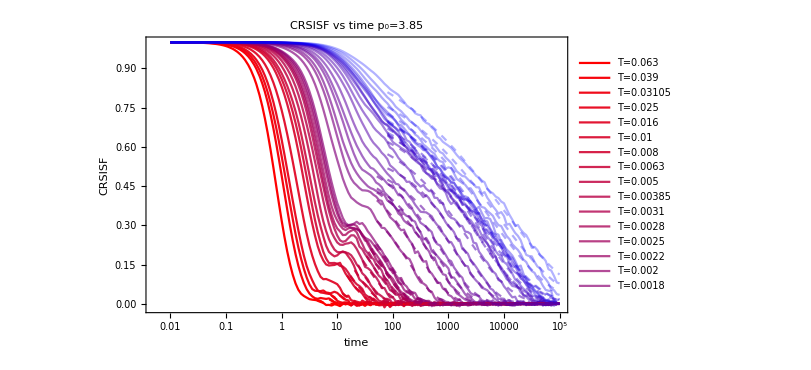

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

Show::gcomb: Could not combine the graphics objects in Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,{}].

#### SISF

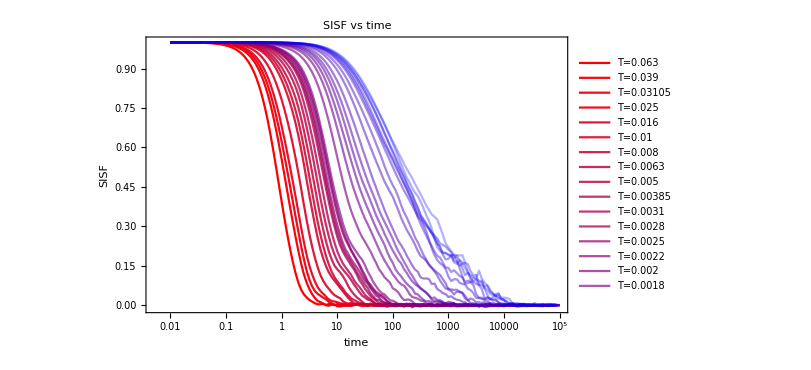

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

```mathematica
time[[40]]
```

Part::partw: Part 40 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

{0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧}⟦40⟧

```mathematica
fitSISFStartPos=fitCRSISFStartPos-5
```

{39,44,44,47,48,50,51,53,54,56,57,58,59,59,60,61,61,61,61,61,61,65,65,65,65,65,65,65,65,65,65}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsSISF
```

{FittedModel[0.964593 ⅇ^(-1.41191 t^0.875504)],FittedModel[0.984679 ⅇ^(-1.08658 t^0.897084)],FittedModel[0.65112 ⅇ^(-0.692349 t^0.897776)],FittedModel[0.863445 ⅇ^(-1.0317 t^0.639523)],FittedModel[0.449592 ⅇ^(-0.360708 t^0.87326)],FittedModel[0.65504 ⅇ^(-0.265978 t^0.899231)],FittedModel[0.560542 ⅇ^(-0.233263 t^0.888657)],FittedModel[0.816716 ⅇ^(-0.203832 t^0.897679)],FittedModel[0.504557 ⅇ^(-0.127353 t^0.899143)],FittedModel[0.578944 ⅇ^(-0.120708 t^0.899186)],FittedModel[0.679024 ⅇ^(-0.108216 t^0.89838)],FittedModel[0.58347 ⅇ^(-0.0920676 t^0.898555)],FittedModel[0.553569 ⅇ^(-0.0798865 t^0.899438)],FittedModel[0.61939 ⅇ^(-0.106923 t^0.807878)],FittedModel[0.99193 ⅇ^(-0.191165 t^0.706116)],FittedModel[0.991834 ⅇ^(-0.169591 t^0.698025)],FittedModel[0.657379 ⅇ^(-0.0825544 t^0.723245)],FittedModel[0.998661 ⅇ^(-0.160001 t^0.561219)],FittedModel[0.999748 ⅇ^(-0.131021 t^0.570866)],FittedModel[0.999941 ⅇ^(-0.128524 t^0.539873)],FittedModel[0.999914 ⅇ^(-0.097305 t^0.577021)],FittedModel[0.999979 ⅇ^(-0.129795 t^0.485515)],FittedModel[0.999987 ⅇ^(-0.0954167 t^0.487873)],FittedModel[0.999991 ⅇ^(-0.0579442 t^0.564838)],FittedModel[0.999993 ⅇ^(-0.0590091 t^0.516263)],FittedModel[0.999997 ⅇ^(-0.0599779 t^0.504646)],FittedModel[0.999997 ⅇ^(-0.0722796 t^0.459346)],FittedModel[0.999998 ⅇ^(-0.0686823 t^0.457224)],FittedModel[0.999998 ⅇ^(-0.0717188 t^0.448959)],FittedModel[0.999999 ⅇ^(-0.0562406 t^0.481949)],FittedModel[0.999998 ⅇ^(-0.0544878 t^0.472498)]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.67436,0.911591,1.50611,0.952369,3.21452,4.3612,5.1447,5.88111,9.89419,10.5007,11.8835,14.2182,16.6049,15.9157,10.4152,12.7049,31.4613,26.1893,35.1702,44.7117,56.7025,67.0497,123.446,154.878,240.284,263.948,304.743,349.907,353.942,392.224,472.62}

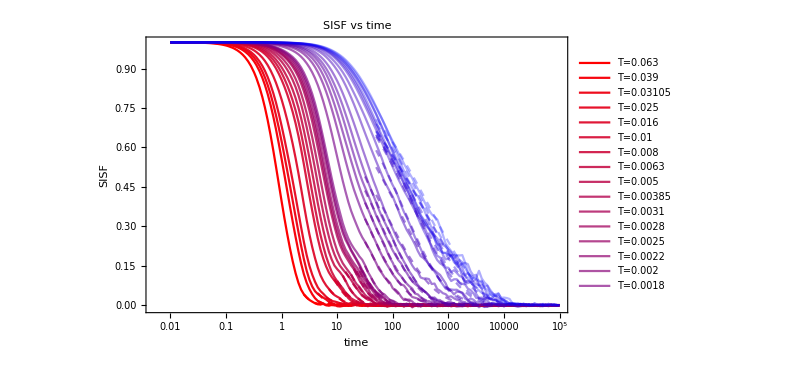

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### Tau Alphas

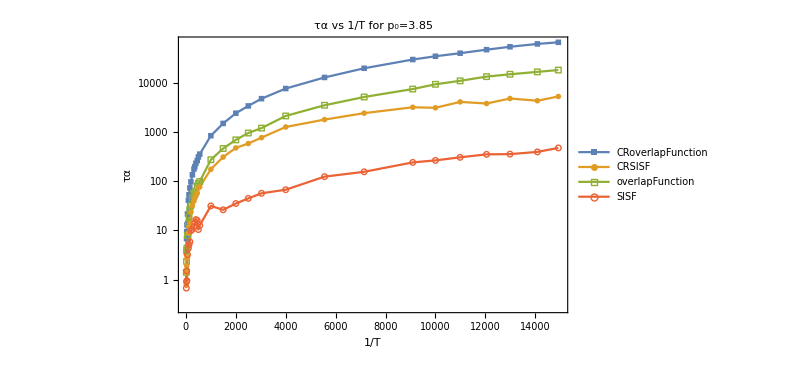

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■"],Style["●"],Style["□"],Style["○"]},ImageSize->600,PlotLabel->"τα vs 1/T for p_0=3.85",Joined->True,PlotRange->{{0,15000},All}]
```

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCRSISFfits[[T]],tauCROverlapfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,0.785881,3.5816,1.40833,0.67436},{0.039,1.39553,6.82841,2.34653,0.911591},{0.03105,1.90531,9.43977,3.95386,1.50611},{0.025,2.6812,13.0053,4.37269,0.952369},{0.016,2.97258,21.5555,7.95333,3.21452},{0.01,8.88937,40.9069,13.9341,4.3612},{0.008,11.5548,53.0556,19.0105,5.1447},{0.0063,13.8183,72.844,26.8103,5.88111},{0.005,23.3053,96.7288,32.028,9.89419},{0.00385,31.7944,134.636,45.6069,10.5007},{0.0031,39.3291,176.108,57.712,11.8835},{0.0028,45.0717,196.975,53.2539,14.2182},{0.0025,52.4582,230.685,62.4043,16.6049},{0.0022,56.8893,261.696,79.6394,15.9157},{0.002,73.2469,310.253,90.4598,10.4152},{0.0018,76.7975,353.828,98.5318,12.7049},{0.001,174.35,836.628,272.464,31.4613},{0.00067,308.528,1485.58,460.1,26.1893},{0.0005,473.423,2393.55,689.534,35.1702},{0.0004,580.788,3366.77,949.332,44.7117},{0.00033,765.103,4726.53,1194.93,56.7025},{0.00025,1258.69,7589.61,2107.15,67.0497},{0.00018,1777.36,12735.1,3471.29,123.446},{0.00014,2401.99,19568.5,5111.19,154.878},{0.00011,3161.46,29435.,7413.19,240.284},{0.0001,3086.83,34307.9,9254.09,263.948},{0.000091,4062.84,39568.6,10883.1,304.743},{0.000083,3769.09,46676.6,13255.5,349.907},{0.000077,4763.,53411.3,14775.7,353.942},{0.000071,4292.74,61062.2,16536.4,392.224},{0.000067,5235.62,65880.6,18017.2,472.62}}

```mathematica
N[Table[1/(i*1000+10000),{i,1,5}]]
```

{0.0000909091,0.0000833333,0.0000769231,0.0000714286,0.0000666667}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP385.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP385.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p385.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

Part::partw: Part 3 of NonlinearModelFit[{},{ⅇ^(-(t Power[«2»])^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification NonlinearModelFit[{},{ⅇ^(-Times[«2»]^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification fitsCRoverlap⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of fitsCRoverlap⟦1⟧[BestFitParameters] does not exist.

Part::partd: Part specification fitsCRoverlap⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of fitsCRoverlap⟦2⟧[BestFitParameters] does not exist.

Part::partd: Part specification fitsCRoverlap⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of fitsCRoverlap⟦3⟧[BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{fitsCRoverlap⟦1⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦2⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦3⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦4⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦5⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦6⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦7⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦8⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦9⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦10⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦11⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦12⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦13⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦14⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦15⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦16⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦17⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦18⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦19⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦20⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦21⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦22⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦23⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦24⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦25⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦26⟧[BestFitParameters]⟦3,2⟧}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification fitsCRoverlap⟦1⟧ is longer than depth of object.

Part::partd: Part specification fitsCRoverlap⟦1⟧[BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification fitsCRoverlap⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{fitsCRoverlap⟦1⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦2⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦3⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦4⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦5⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦6⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦7⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦8⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦9⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦10⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦11⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦12⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦13⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦14⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦15⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦16⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦17⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦18⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦19⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦20⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦21⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦22⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦23⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦24⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦25⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦26⟧[BestFitParameters]⟦1,2⟧}

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

tauCRSISFAllT

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

TlistAllT

```mathematica
TlistAllT
```

TlistAllT

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

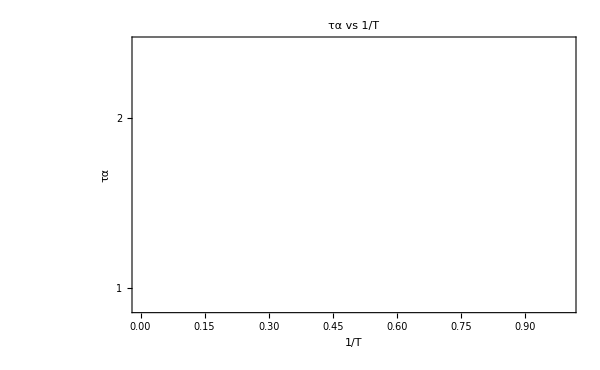

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

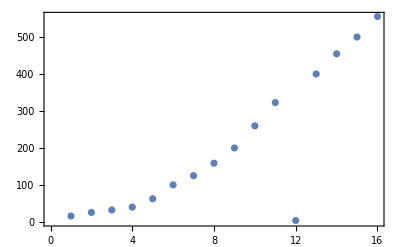

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16